```mathematica
<<myFunctionsMathematica8.m
```

{Temporary}

```mathematica
stream4=OpenRead["loglinearparameters20may16no1"];
model=ReadList[stream4];
Close[stream4];
mdata={};
bdata={};
For[k=0,k<Length[model],k++;
n=model[[k,1]];
m=model[[k,2]];
b=model[[k,3]];
mdatum={n,m};
mdata=Append[mdata,mdatum];
bdatum={n,b};
bdata=Append[bdata,bdatum]];
Print["slopes"];
Print[ListPlot[mdata]];
Print["intercepts"];
Print[ListPlot[bdata]]
```

## leaf5point11left

slopes

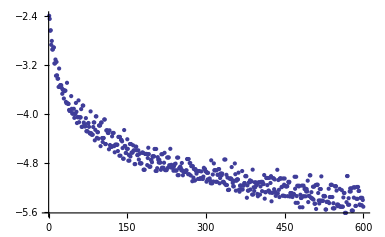

intercepts

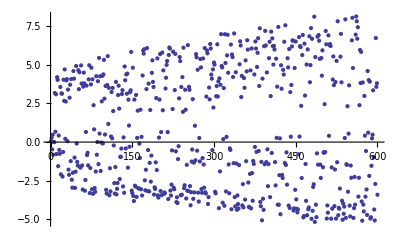

```mathematica
leaf5point11right
```